```mathematica
ClearAll["Global`*"]
```

```mathematica
$RecursionLimit=10000
```

10000

```mathematica
K[n_] := If[ n==1,0,FullSimplify[MangoldtLambda[n]/Log[n]]]
pk[n_] := If[ K[n]==0,0,-((2^(1/K[n])-1) (K[n]^1))]
F[n_,0]:=1; F[n_,k_] := F[n,k]=Sum[ pk[j] F[Floor[n/j],k-1],{j,2,n}]
f[n_, k_] := f[n,k] = F[n,k]-F[n-1,k];f[1,0]:=1
pp[n_,z_] := pp[n,z]=Sum[ z^k/k! f[n,k],{k,0,Log[2,n]}]
PP[n_,z_] := PP[n,z]=Sum[ pp[j,z],{j,1,n}]
```

```mathematica
F[100,1]
```

-898/15

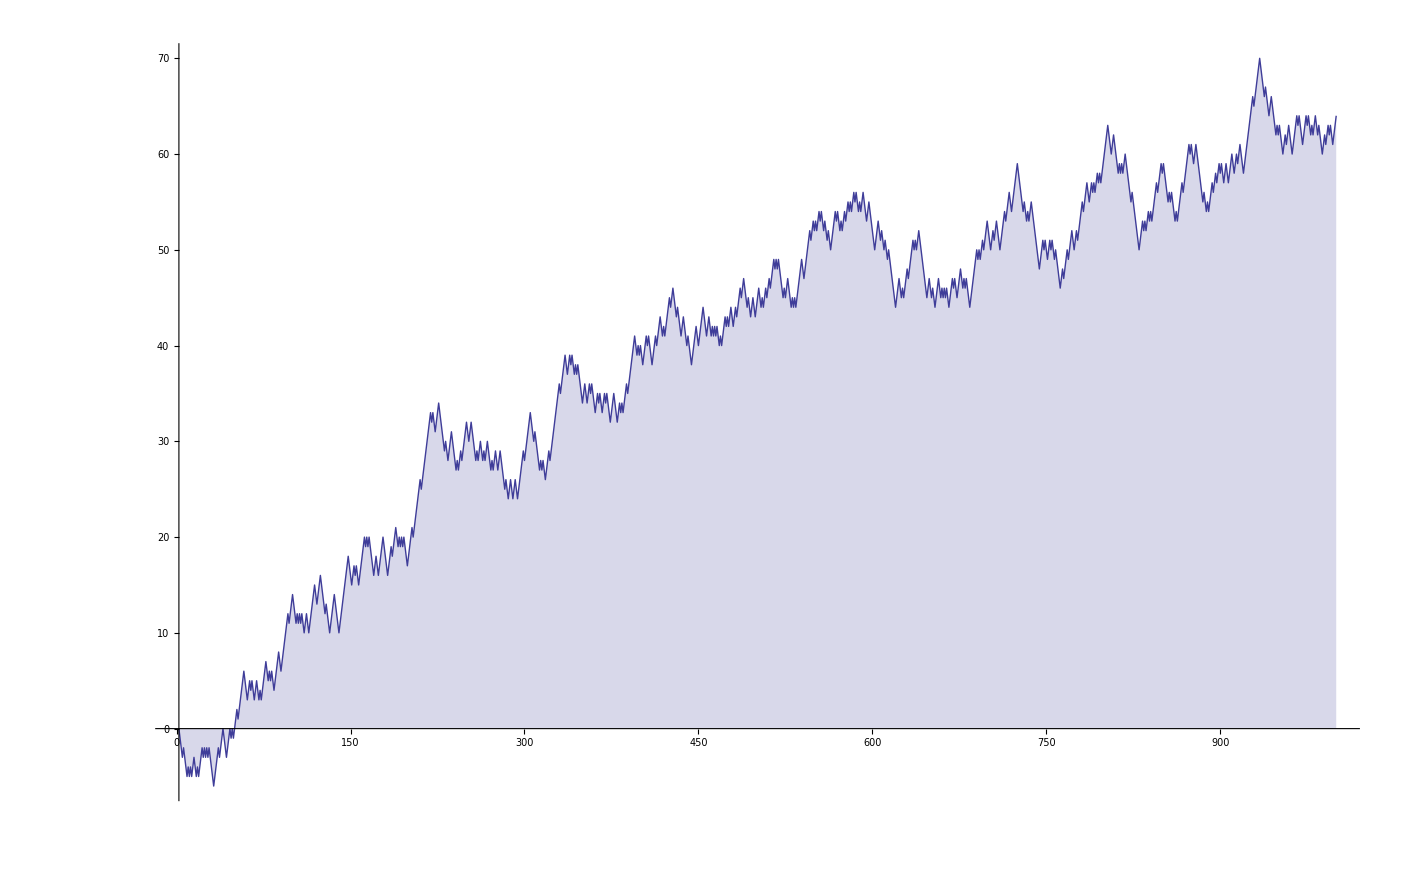

```mathematica
DiscretePlot[ PP[n,1],{n,2,1000}]
```

```mathematica
F[1,1]
```

0

```mathematica
Table[ {n, pp[n,1], pp[n,-1]},{n,1,100}]//TableForm
```

1 | 1 | 1
2 | -1 | 1
3 | -1 | 1
4 | -1 | 2
5 | -1 | 1
6 | 1 | 1
7 | -1 | 1
8 | -1 | 4
9 | -1 | 2
10 | 1 | 1
11 | -1 | 1
12 | 1 | 2
13 | -1 | 1
14 | 1 | 1
15 | 1 | 1
16 | -1 | 8
17 | -1 | 1
18 | 1 | 2
19 | -1 | 1
20 | 1 | 2
21 | 1 | 1
22 | 1 | 1
23 | -1 | 1
24 | 1 | 4
25 | -1 | 2
26 | 1 | 1
27 | -1 | 4
28 | 1 | 2
29 | -1 | 1
30 | -1 | 1
31 | -1 | 1
32 | -1 | 16
33 | 1 | 1
34 | 1 | 1
35 | 1 | 1
36 | 1 | 4
37 | -1 | 1
38 | 1 | 1
39 | 1 | 1
40 | 1 | 4
41 | -1 | 1
42 | -1 | 1
43 | -1 | 1
44 | 1 | 2
45 | 1 | 2
46 | 1 | 1
47 | -1 | 1
48 | 1 | 8
49 | -1 | 2
50 | 1 | 2
51 | 1 | 1
52 | 1 | 2
53 | -1 | 1
54 | 1 | 4
55 | 1 | 1
56 | 1 | 4
57 | 1 | 1
58 | 1 | 1
59 | -1 | 1
60 | -1 | 2
61 | -1 | 1
62 | 1 | 1
63 | 1 | 2
64 | -1 | 32
65 | 1 | 1
66 | -1 | 1
67 | -1 | 1
68 | 1 | 2
69 | 1 | 1
70 | -1 | 1
71 | -1 | 1
72 | 1 | 8
73 | -1 | 1
74 | 1 | 1
75 | 1 | 2
76 | 1 | 2
77 | 1 | 1
78 | -1 | 1
79 | -1 | 1
80 | 1 | 8
81 | -1 | 8
82 | 1 | 1
83 | -1 | 1
84 | -1 | 2
85 | 1 | 1
86 | 1 | 1
87 | 1 | 1
88 | 1 | 4
89 | -1 | 1
90 | -1 | 2
91 | 1 | 1
92 | 1 | 2
93 | 1 | 1
94 | 1 | 1
95 | 1 | 1
96 | 1 | 16
97 | -1 | 1
98 | 1 | 2
99 | 1 | 2
100 | 1 | 4

```mathematica
Expand[(2^(1/rr[n])-1) rr[n]]
```

-rr[n]+2^(1/rr[n]) rr[n]